# Домашняя контрольная работа по химии твердого тела

Александр Нехаев

Январь 2021

## Задача 1

Даны длины сторон элементарных ячеек веществ, имеющих структуру каменной соли: MgS (5.193 Å), CaS (5.684 Å), SrS (6.020 Å), BaS (6.375 Å). Определите радиус катиона для всех случаев. Чтобы рассчитать радиус S^-2, предположите, что в MgS ионы S^-2 находятся в прямом контакте.

### Решение

Катион - полжительно заряженный ион. Кристаллическая структура у всех соединений кубическая. Таким образом a - это расстояние между катионом и анионом.

```mathematica
materials={Entity["Chemical","MagnesiumSulfide"],Entity["Chemical","CalciumSulfide"],Entity["Chemical","StrontiumSulfide"],Entity["Chemical","BariumSulfide"]};
a={Quantity[5.193, "Angstroms"],Quantity[5.684, "Angstroms"],Quantity[6.02, "Angstroms"],Quantity[6.375, "Angstroms"]};
crystalStructure=Table[Entity["CrystalFamily","Cubic"],{i,4}];
data=Dataset@(Association/@({Association[{"Material"->#}]&/@materials,
Association[{"A"->#}]&/@a,
Association[{"Structure"->#}]&/@crystalStructure
}ᵀ))
```

Тогда можно ввести связь между длиной стороны элементарной ячейки и радиусом аниона в случае магния (у него ионы серы находятся в прямом контакте):

(2 R_A)^2== 2(A/2)^2

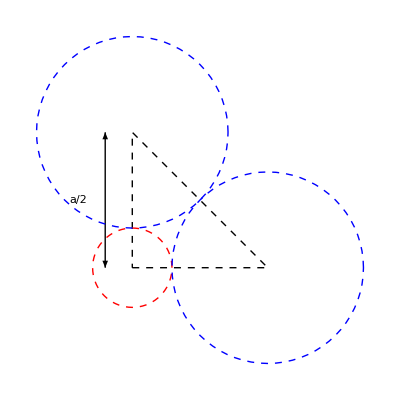

```mathematica
l=1;
d=√(2 l^2);
sch=Graphics[
{Text[Style["a/2",Medium],{-0.4,l/2}],
Arrowheads[{-.05,0.05}],
Arrow[{{-0.2,0},{-0.2,l}}],
Dashed,Line[{{0,0},{l,0},{0,l},{0,0}}],
Thick,Red,Circle[{0,0},l-d/2],
Blue,Circle[{l,0},d/2],
Blue,Circle[{0,l},d/2]
}
];
lattice=Graphics3D[
{
Red,Ball[{0,0,0},1-d/2],
Blue,Ball[{0,1,0},d/2],
Red,Ball[{0,2,0},1-d/2],
Blue,Ball[{0,0,1},d/2],
Red,Ball[{0,1,1},1-d/2],
Blue,Ball[{0,2,1},d/2],
Red,Ball[{0,0,2},1-d/2],
Blue,Ball[{0,1,2},d/2],
Red,Ball[{0,2,2},1-d/2],
Blue,Ball[{1,0,0},d/2],
Red,Ball[{1,1,0},1-d/2],
Blue,Ball[{1,2,0},d/2],
Red,Ball[{1,0,1},1-d/2],
Blue,Ball[{1,1,1},d/2],
Red,Ball[{1,2,1},1-d/2],
Blue,Ball[{1,0,2},d/2],
Red,Ball[{1,1,2},1-d/2],
Blue,Ball[{1,2,2},d/2],
Red,Ball[{2,0,0},1-d/2],
Blue,Ball[{2,1,0},d/2],
Red,Ball[{2,2,0},1-d/2],
Blue,Ball[{2,0,1},d/2],
Red,Ball[{2,1,1},1-d/2],
Blue,Ball[{2,2,1},d/2],
Red,Ball[{2,0,2},1-d/2],
Blue,Ball[{2,1,2},d/2],
Red,Ball[{2,2,2},1-d/2]
},
PlotRegion->{{0,1}}
]/.{1-d/2->d/2,d/2->1-d/2,Blue->Red,Red->Blue};
GraphicsGrid[{{lattice,sch}}]
```

Тогда выражение для катиона имеет вид

R_C=A/2-R_A

Выражение для радиуса аниона:

```mathematica
Reduce[(2 Subscript[R, "a"])^2==2(A/2)^2,Subscript[R, "a"]][[2]]//TraditionalForm
```

R_a==A/(2 √2)

Однако, как видно из значений величины a, размер ячейки в остальных кристаллах увеличивается. Анионы остаются неизменными (S^(2-)), но теперь они не соприкасаются. Анион с катионом по прежнему соприкасаются, поэтому зная ионный радиус S^(2-) мы можем найти радиусы катионов как

R_c=A/2-R_a

Результаты:

```mathematica
raS2=data[1,"A"]/(2 √2);
Print["Радиус S^(2-): ",raS2]
Normal@{StringTake[ChemicalData[#,"FormulaString"],2]&/@data[All,"Material"], (Normal@data[All, "A"])/2 - raS2}//Transpose//Dataset
```

Радиус S^(2-): 1.836 Å

## Задача 2

Объясните, почему расчеты энергии кристаллической решетки при учете чисто кулоновских взаимодействий повторяют экспериментальные значения с точностью до 1 % для RbCl и только 10 % для AgCl. Оба соединения обладают структурой каменной соли.

### Решение

Кроме кулоновского взаимодействия, в энергию ионного кристала вносяи вклад такиже энергия отталкивания. Радиус атома  Ag меньше, чем энергия Rb примерно в 1.7 раза, следовательно энергия отталкивания у рубидия будет меньше, тогда вклад в полную энергию будет меньше и тогда учет только кулоновского притяжения будет ближе к эксперименту.

## Задача 3

На рисунке приведена плотность состояний для соединений  Na_x Si_136 – т.н. клатратов, в которых сложный ковалентно-связанный каркас кремния инкорпорирует Na^+. Определите:
- тип проводимости соединения
- характер изменения электронной структуры вблизи уровня Ферми с увеличением содержания Na.
- предположите, что произойдет при уменьшении содержания Na до нуля.

-Graphics-

### Решение

По графикам видно, что ширина запрещенной зоны составляет  ~1 эВ. Отсюда следует, что это полупроводник.
Уровень Ферми находится в зоне проводимости. Тогда тип проводимости электронный и ионы Na - доноры.

Увеличение содержания Na приводит к уменьшению ширины запрещенной зоны и увеличивается значение уровня Ферми.

При уменьшении содержания Na произойдет увеличение запрещенной зоны до ~1.1 эВ, уровень Ферми будет находиться примерно в середине запрещенной зоны.

## Задача 4

Изобразите схематично в координатах температура - состав фазовую диаграмму системы хлорид калия (t_пл = 776°С) – хлорид лития (t_пл= 614°C), эвтектической точкой при 40 мол.% KCl и t = 352°С и твердыми растворами LiCl/KCl с граничными составами Li_0.94 K_0.06 Cl и Li_0.07 K_0.93 Cl. Ответьте на следующие вопросы:
-Почему при получении металлического лития электролизом расплава используют смесь хлоридов лития и калия, а не чистый хлорид лития?
-Каков состав расплава, если при его охлаждении вначале кристаллизуется хлорид калия (точнее, твердый раствор на его основе)?
-Укажите состав фаз в эвтектической точке.
-Каково число степеней свободы в этой точке (считайте P = Const)?

### Решение

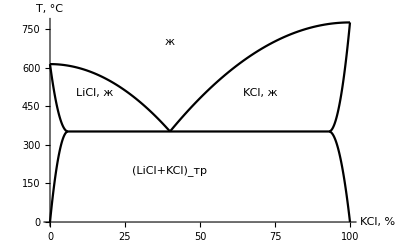

```mathematica
left1=Plot[614-(131 x^2)/800,{x,0,40}];
right1=Plot[-3616/9+(212 x)/9-(53 x^2)/450,{x,40,100}];
left2=Plot[614-(262 x)/3+(131 x^2)/18,{x,0,6}];
right2=Plot[3684424/49-(78864 x)/49+(424 x^2)/49,{x,93,100}];
labels={Text["LiCl, ж",{15,500}],Text["KCl, ж",{70,500}],Text["(LiCl+KCl)_(:0442:0440)",{40,200}],Text["ж",{40,700}]};
left3=Plot[(352 x)/3-(88 x^2)/9,{x,0,6},AxesLabel->{"KCl, %","T, °C"},Epilog->labels];
right3=Plot[-3027200/49+(65472 x)/49-(352 x^2)/49,{x,93,100}];
mid=Plot[352,{x,6,93}];
plots={left3,right1,left2,right2,left1,right3,mid};
Show[plots,PlotRange->Full]
```

Для получения лития используют смесь хлорида лития и хлорида калия поскольку в таком виде температура плавления будет ниже.

Исходя их фазовой диаграммы содержание KCl превышает 40%.

Жидкая и твердые фазы LiCl и KCl.

Согласно правилу фаз C=K-Φ+n, где  K - число компонентов, Φ - число фаз, n - число степеней свобод (температура/давление). Поскольку давление постоянное, принимаем n=1. Тогда: C=K-Ф+n=2-3+1=0.

## Задача 5

Перед Вами поставили задачу: получить пироэлектрик допированием  CeO_2. Соединение должно остаться изолятором, но при этом приобрести пироэлектрические свойства. Предложите допирующие агенты (обязательно обоснуйте выбор!)
-план эксперимента
-план исследования полученных материалов

### Решение

Пироэлектрики обладают спонтанной поляризацией. Её присутствие возможно в кристаллах с направленной симметрией. Симметрия у CeO_2 mOverBar[3]m, таким образом её нужно помнять, чтобы появилось направление. Для этого нужно допировать ионами с другим радиусом (нарпимер большим). Например ионом серы S^(2-).
Значения ионных радиусов для кислорода и серы составляют 140 пм и 184 пм соотвественно.

Возможные методы легирования:

Спекание сульфида и оксда церия

Ионная имплантация

Возможные методы исследования:

Рентгеновская диффракция

Электронная сканирующая микроскопия

Измерение удельной проводимости при изменении температуры.